```mathematica
(*  QUESTION 1 - 10 points  *)

(*initializing recurrence relation of Chebyshev polynomials*)
T[0, x_] := 1;
T[1, x_] := x;

(*rewriting given recursive formula from T_{n+1}(x) to T_{n}(x)*)
T[n_, x_] := T[n, x] = 2 x T[n - 1, x] - T[n - 2, x];

(*Generate Chebyshev polynomials using recurrence relation up to n = 10 *)
Recurrence := Table[T[n, x], {n, 0, 10}]
Expand[Recurrence]

(*Generate Chebyshev polynomials using closed form up to n = 10 *)
ClosedForm = Table[Cos[n ArcCos[x]], {n, 0, 10}]

(*verify that closed form and recurrence form are equivalent*)
verification = Simplify[Recurrence == ClosedForm]

(*verify that built in function and recurrence form (and thus also closed form) are equivalent*)
chebyshevBuiltIn = Table[ChebyshevT[n, x], {n, 0, 10}];
verifyBuiltIn = Simplify[Recurrence == chebyshevBuiltIn]
```

{1,x,-1+2 x^2,-3 x+4 x^3,1-8 x^2+8 x^4,5 x-20 x^3+16 x^5,-1+18 x^2-48 x^4+32 x^6,-7 x+56 x^3-112 x^5+64 x^7,1-32 x^2+160 x^4-256 x^6+128 x^8,9 x-120 x^3+432 x^5-576 x^7+256 x^9,-1+50 x^2-400 x^4+1120 x^6-1280 x^8+512 x^10}

{1,x,Cos[2 ArcCos[x]],Cos[3 ArcCos[x]],Cos[4 ArcCos[x]],Cos[5 ArcCos[x]],Cos[6 ArcCos[x]],Cos[7 ArcCos[x]],Cos[8 ArcCos[x]],Cos[9 ArcCos[x]],Cos[10 ArcCos[x]]}

True

True

```mathematica
(*  QUESTION 2 - 5 points  *)

(* First derivatives *)
firstDerivativesRecurrence = Table[D[Recurrence[[n]], x], {n, 1, 11}];

(* Second derivatives *)
secondDerivativesRecurrence = Table[D[Recurrence[[n]], {x, 2}], {n, 1, 11}];

(* Tabulate results *)
data = Table[{n - 1, Recurrence[[n]], firstDerivativesRecurrence[[n]], secondDerivativesRecurrence[[n]]}, {n, 1, 11}];

(* Display results in table format *)
TableForm[Expand[data], TableHeadings -> {None, {"n", "T_n(x)", "T_n'(x)", "T_n''(x)"}}]

(* First derivatives *)
firstDerivatives = Table[D[ClosedForm[[n]], x], {n, 1, 11}];

(* Second derivatives *)
secondDerivatives = Table[D[ClosedForm[[n]], {x, 2}], {n, 1, 11}];

(* Tabulate results *)
data2 = Table[{n - 1, ClosedForm[[n]], firstDerivatives[[n]], secondDerivatives[[n]]}, {n, 1, 11}];

(* Display results in table format *)
TableForm[data2, TableHeadings -> {None, {"n", "T_n(x)", "T_n'(x)", "T_n''(x)"}}]
```

n | T_n(x) | T_n'(x) | T_n''(x)
0 | 1 | 0 | 0
1 | x | 1 | 0
2 | -1+2 x^2 | 4 x | 4
3 | -3 x+4 x^3 | -3+12 x^2 | 24 x
4 | 1-8 x^2+8 x^4 | -16 x+32 x^3 | -16+96 x^2
5 | 5 x-20 x^3+16 x^5 | 5-60 x^2+80 x^4 | -120 x+320 x^3
6 | -1+18 x^2-48 x^4+32 x^6 | 36 x-192 x^3+192 x^5 | 36-576 x^2+960 x^4
7 | -7 x+56 x^3-112 x^5+64 x^7 | -7+168 x^2-560 x^4+448 x^6 | 336 x-2240 x^3+2688 x^5
8 | 1-32 x^2+160 x^4-256 x^6+128 x^8 | -64 x+640 x^3-1536 x^5+1024 x^7 | -64+1920 x^2-7680 x^4+7168 x^6
9 | 9 x-120 x^3+432 x^5-576 x^7+256 x^9 | 9-360 x^2+2160 x^4-4032 x^6+2304 x^8 | -720 x+8640 x^3-24192 x^5+18432 x^7
10 | -1+50 x^2-400 x^4+1120 x^6-1280 x^8+512 x^10 | 100 x-1600 x^3+6720 x^5-10240 x^7+5120 x^9 | 100-4800 x^2+33600 x^4-71680 x^6+46080 x^8

n | T_n(x) | T_n'(x) | T_n''(x)
0 | 1 | 0 | 0
1 | x | 1 | 0
2 | Cos[2 ArcCos[x]] | (2 Sin[2 ArcCos[x]])/(√(1-x^2)) | -(4 Cos[2 ArcCos[x]])/(1-x^2)+(2 x Sin[2 ArcCos[x]])/((1-x^2)^(3/2))
3 | Cos[3 ArcCos[x]] | (3 Sin[3 ArcCos[x]])/(√(1-x^2)) | -(9 Cos[3 ArcCos[x]])/(1-x^2)+(3 x Sin[3 ArcCos[x]])/((1-x^2)^(3/2))
4 | Cos[4 ArcCos[x]] | (4 Sin[4 ArcCos[x]])/(√(1-x^2)) | -(16 Cos[4 ArcCos[x]])/(1-x^2)+(4 x Sin[4 ArcCos[x]])/((1-x^2)^(3/2))
5 | Cos[5 ArcCos[x]] | (5 Sin[5 ArcCos[x]])/(√(1-x^2)) | -(25 Cos[5 ArcCos[x]])/(1-x^2)+(5 x Sin[5 ArcCos[x]])/((1-x^2)^(3/2))
6 | Cos[6 ArcCos[x]] | (6 Sin[6 ArcCos[x]])/(√(1-x^2)) | -(36 Cos[6 ArcCos[x]])/(1-x^2)+(6 x Sin[6 ArcCos[x]])/((1-x^2)^(3/2))
7 | Cos[7 ArcCos[x]] | (7 Sin[7 ArcCos[x]])/(√(1-x^2)) | -(49 Cos[7 ArcCos[x]])/(1-x^2)+(7 x Sin[7 ArcCos[x]])/((1-x^2)^(3/2))
8 | Cos[8 ArcCos[x]] | (8 Sin[8 ArcCos[x]])/(√(1-x^2)) | -(64 Cos[8 ArcCos[x]])/(1-x^2)+(8 x Sin[8 ArcCos[x]])/((1-x^2)^(3/2))
9 | Cos[9 ArcCos[x]] | (9 Sin[9 ArcCos[x]])/(√(1-x^2)) | -(81 Cos[9 ArcCos[x]])/(1-x^2)+(9 x Sin[9 ArcCos[x]])/((1-x^2)^(3/2))
10 | Cos[10 ArcCos[x]] | (10 Sin[10 ArcCos[x]])/(√(1-x^2)) | -(100 Cos[10 ArcCos[x]])/(1-x^2)+(10 x Sin[10 ArcCos[x]])/((1-x^2)^(3/2))

```mathematica
(* Used to verify C code for Question 3 *)

(*creates a list of 100 points from -1 to 1 of equal size*)
points=Subdivide[-1, 1, 100];

(* Define the function *)
T10[x_] := Cos[10 ArcCos[x]];

(* Define the first derivative function with a safeguard for infinity or undefined *)
T10prime[x_] := If[Abs[x] == 1, "Undefined", (10 Sin[10 ArcCos[x]])/(√(1-x^2))];
(* Define the second derivative function with a safeguard for infinity or undefined *)
T10doubleprime[x_] := If[Abs[x] == 1, "Undefined", -(100 Cos[10 ArcCos[x]])/(1-x^2)+(10 x Sin[10 ArcCos[x]])/((1-x^2)^(3/2))];
(*evaluating the functions using the point list*)
T10Values = T10 /@ points;
T10primeValues = T10prime /@ points;
T10doubleprimeValues = T10doubleprime /@ points;

(* Combine the results into a table using the index to access values from the lists *)
results = Table[ {points[[i]], T10Values[[i]], T10primeValues[[i]], T10doubleprimeValues[[i]]}, {i, 1, Length[points]}];

(* Display the results in a table form *)
TableForm[N[results], TableHeadings -> {None, {"x", "T10(x)", "T10'(x)", "T10''(x)"}}]
```

x | T10(x) | T10'(x) | T10''(x)
-1. | 1. | Undefined | Undefined
-0.98 | -0.419189 | -45.6236 | 2187.63
-0.96 | -0.954251 | -10.6788 | 1347.92
-0.94 | -0.942732 | 9.77655 | 730.956
-0.92 | -0.632852 | 19.756 | 293.683
-0.9 | -0.200747 | 22.4746 | -0.801843
-0.88 | 0.234741 | 20.4655 | -183.882
-0.86 | 0.599501 | 15.6846 | -282.023
-0.84 | 0.85354 | 9.60266 | -317.324
-0.82 | 0.98213 | 3.28817 | -308.026
-0.8 | 0.988497 | -2.52072 | -268.981
-0.78 | 0.887862 | -7.3526 | -212.082
-0.76 | 0.702675 | -10.9476 | -146.655
-0.74 | 0.458869 | -13.2099 | -79.8223
-0.72 | 0.183004 | -14.1664 | -16.8202
-0.7 | -0.0998401 | -13.9328 | 38.7
-0.68 | -0.367533 | -12.6841 | 84.4094
-0.66 | -0.601833 | -10.6304 | 119.063
-0.64 | -0.788889 | -7.99786 | 142.289
-0.62 | -0.919401 | -5.01301 | 154.399
-0.6 | -0.988497 | -1.89054 | 156.225
-0.58 | -0.995405 | 1.17542 | 148.973
-0.56 | -0.942979 | 4.01757 | 134.103
-0.54 | -0.837112 | 6.4994 | 113.215
-0.52 | -0.686104 | 8.51711 | 87.9681
-0.5 | -0.5 | 10. | 60.
-0.48 | -0.289934 | 10.9094 | 30.8692
-0.46 | -0.0675116 | 11.2366 | 2.00701
-0.44 | 0.155765 | 11. | -25.3181
-0.42 | 0.369003 | 10.2414 | -50.0263
-0.4 | 0.562346 | 9.02224 | -71.2423
-0.38 | 0.727332 | 7.41942 | -88.3036
-0.36 | 0.85715 | 5.52083 | -100.761
-0.34 | 0.946825 | 3.42132 | -108.374
-0.32 | 0.993314 | 1.21851 | -111.098
-0.3 | 0.995523 | -0.990889 | -109.071
-0.28 | 0.954251 | -3.11465 | -102.597
-0.26 | 0.872075 | -5.06803 | -92.1169
-0.24 | 0.753166 | -6.77635 | -78.1943
-0.22 | 0.603073 | -8.1772 | -61.4842
-0.2 | 0.428456 | -9.22195 | -42.7096
-0.18 | 0.236797 | -9.87691 | -22.6353
-0.16 | 0.0361024 | -10.1239 | -2.0427
-0.14 | -0.165418 | -9.96033 | 18.2949
-0.12 | -0.359654 | -9.39877 | 37.6352
-0.1 | -0.538893 | -8.46618 | 55.2888
-0.08 | -0.696093 | -7.20261 | 70.6375
-0.06 | -0.825132 | -5.6596 | 83.1521
-0.04 | -0.921019 | -3.89829 | 92.4057
-0.02 | -0.980064 | -1.98722 | 98.0854
0. | -1. | 0. | 100.
0.02 | -0.980064 | 1.98722 | 98.0854
0.04 | -0.921019 | 3.89829 | 92.4057
0.06 | -0.825132 | 5.6596 | 83.1521
0.08 | -0.696093 | 7.20261 | 70.6375
0.1 | -0.538893 | 8.46618 | 55.2888
0.12 | -0.359654 | 9.39877 | 37.6352
0.14 | -0.165418 | 9.96033 | 18.2949
0.16 | 0.0361024 | 10.1239 | -2.0427
0.18 | 0.236797 | 9.87691 | -22.6353
0.2 | 0.428456 | 9.22195 | -42.7096
0.22 | 0.603073 | 8.1772 | -61.4842
0.24 | 0.753166 | 6.77635 | -78.1943
0.26 | 0.872075 | 5.06803 | -92.1169
0.28 | 0.954251 | 3.11465 | -102.597
0.3 | 0.995523 | 0.990889 | -109.071
0.32 | 0.993314 | -1.21851 | -111.098
0.34 | 0.946825 | -3.42132 | -108.374
0.36 | 0.85715 | -5.52083 | -100.761
0.38 | 0.727332 | -7.41942 | -88.3036
0.4 | 0.562346 | -9.02224 | -71.2423
0.42 | 0.369003 | -10.2414 | -50.0263
0.44 | 0.155765 | -11. | -25.3181
0.46 | -0.0675116 | -11.2366 | 2.00701
0.48 | -0.289934 | -10.9094 | 30.8692
0.5 | -0.5 | -10. | 60.
0.52 | -0.686104 | -8.51711 | 87.9681
0.54 | -0.837112 | -6.4994 | 113.215
0.56 | -0.942979 | -4.01757 | 134.103
0.58 | -0.995405 | -1.17542 | 148.973
0.6 | -0.988497 | 1.89054 | 156.225
0.62 | -0.919401 | 5.01301 | 154.399
0.64 | -0.788889 | 7.99786 | 142.289
0.66 | -0.601833 | 10.6304 | 119.063
0.68 | -0.367533 | 12.6841 | 84.4094
0.7 | -0.0998401 | 13.9328 | 38.7
0.72 | 0.183004 | 14.1664 | -16.8202
0.74 | 0.458869 | 13.2099 | -79.8223
0.76 | 0.702675 | 10.9476 | -146.655
0.78 | 0.887862 | 7.3526 | -212.082
0.8 | 0.988497 | 2.52072 | -268.981
0.82 | 0.98213 | -3.28817 | -308.026
0.84 | 0.85354 | -9.60266 | -317.324
0.86 | 0.599501 | -15.6846 | -282.023
0.88 | 0.234741 | -20.4655 | -183.882
0.9 | -0.200747 | -22.4746 | -0.801843
0.92 | -0.632852 | -19.756 | 293.683
0.94 | -0.942732 | -9.77655 | 730.956
0.96 | -0.954251 | 10.6788 | 1347.92
0.98 | -0.419189 | 45.6236 | 2187.63
1. | 1. | Undefined | Undefined

Equation for T10' error fit:FittedModel[…]

R^2 value for T10' error fit: 0.930433

Equation for T10'' error fit: FittedModel[…]

R^2 value for T10'' error fit: 0.974511

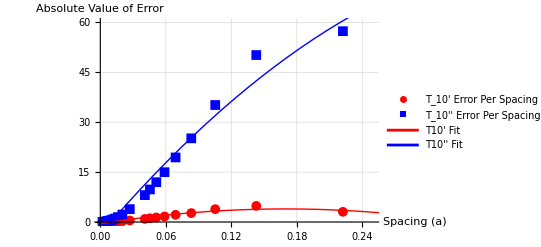

```mathematica
(* QUESTION 6 - 15 points *)

(* Define points list and errors *)
PointsList = {9, 14, 19, 24, 29, 34, 39, 44, 49, 74, 99, 124, 149, 174, 199, 249, 274, 299, 349, 499, 998};
SpacingsList = 2.0 / # & /@ PointsList;

(*T10' Errors, given by question5.c file*)
T10primeErrors = {3.068475, 4.843842, 3.863943, 2.684250, 2.162683, 1.679828, 1.360720, 1.119144, 0.928909, 0.453909, 
  0.267358, 0.175757, 0.124243, 0.092429, 0.071432, 0.046315, 0.038458, 0.032443, 0.023983, 0.011883, 0.003015};

(*T10'' Errors, given by question5.c file*)
T10doubleprimeErrors = {57.367208, 50.194157, 35.174128, 25.156882, 19.409288, 14.979475, 11.967991, 9.785257, 8.086310, 
  3.871511, 2.258322, 1.475986, 1.039465, 0.771242, 0.594841, 0.384608, 0.319035, 0.268902, 0.198512, 0.098114, 0.024826};

(*Create paired lists for plotting *)
primeErrorsData = Transpose[{SpacingsList, T10primeErrors}];
doubleprimeErrorsData = Transpose[{SpacingsList, T10doubleprimeErrors}];

(* Fit the data using LinearModelFit *)
fitPrimeModel = LinearModelFit[primeErrorsData, {1, x, x^2}, x];
fitDoublePrimeModel = LinearModelFit[doubleprimeErrorsData, {1, x, x^2}, x];

(* Extract R^2 values from the fits *)
rSquaredPrime = fitPrimeModel["RSquared"];
rSquaredDoublePrime = fitDoublePrimeModel["RSquared"];

(* Print the equations of the best fits and R^2 values *)
Print["Equation for T10' error fit:", fitPrimeModel];
Print["\nR^2 value for T10' error fit: ", rSquaredPrime];
Print["\nEquation for T10'' error fit: ", fitDoublePrimeModel];
Print["\nR^2 value for T10'' error fit: ", rSquaredDoublePrime, "\n"];

(* Generate the fitted lines as Plot objects *)
fitPrimeLine = Plot[fitPrimeModel[x], {x, 0, 0.6}, PlotStyle -> {Red, Thick}, PlotLegends -> {"T10' Fit"}];
fitDoublePrimeLine = Plot[fitDoublePrimeModel[x], {x, 0, 0.6}, PlotStyle -> {Blue, Thick}, PlotLegends -> {"T10'' Fit"}];

(* Plot both sets of errors with labels and styling *)
Show[
  ListPlot[
    {primeErrorsData, doubleprimeErrorsData},
    PlotLegends -> {"T_10' Error Per Spacing", "T_10'' Error Per Spacing"},
    AxesLabel -> {"Spacing (a)", "Absolute Value of Error"},
    PlotRange -> {{0, 0.25}, {0, 60}},  (* Adjust the x-axis and y-axis ranges as needed *)
    PlotStyle -> {Red, Blue},
    PlotMarkers -> {Automatic, 10},
    GridLines -> Automatic
  ],
  fitPrimeLine,
  fitDoublePrimeLine
]
```

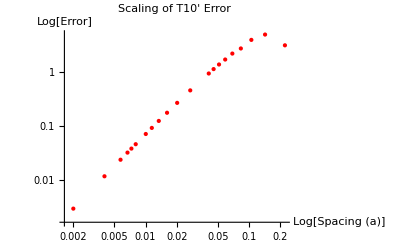

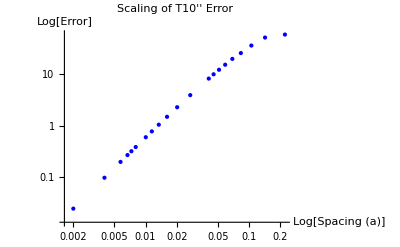

Slope for T10' errors: 1.65495

Slope for T10'' errors: 1.74296

```mathematica
(* Log-log plot of errors *)
logPrimeErrors = ListLogLogPlot[
  Transpose[{SpacingsList, T10primeErrors}],
  PlotStyle -> {Red, PointSize[Medium]},
  AxesLabel -> {"Log[Spacing (a)]", "Log[Error]"},
  PlotLabel -> "Scaling of T10' Error",
  GridLines -> Automatic
];

logDoublePrimeErrors = ListLogLogPlot[
  Transpose[{SpacingsList, T10doubleprimeErrors}],
  PlotStyle -> {Blue, PointSize[Medium]},
  AxesLabel -> {"Log[Spacing (a)]", "Log[Error]"},
  PlotLabel -> "Scaling of T10'' Error",
  GridLines -> Automatic
];

(* Show the plots *)
Print[logPrimeErrors];
Print[logDoublePrimeErrors];

(* Calculate log-log values *)
logSpacings = Log10[SpacingsList];
logPrimeErrors = Log10[T10primeErrors];
logDoublePrimeErrors = Log10[T10doubleprimeErrors];

(* Estimate slope using linear regression *)
primeFit = LinearModelFit[Transpose[{logSpacings, logPrimeErrors}], x, x];
doublePrimeFit = LinearModelFit[Transpose[{logSpacings, logDoublePrimeErrors}], x, x];

(* Extract slopes *)
primeSlope = primeFit["BestFitParameters"][[2]];
doublePrimeSlope = doublePrimeFit["BestFitParameters"][[2]];

(* Print results *)
Print["Slope for T10' errors: ", primeSlope];
Print["Slope for T10'' errors: ", doublePrimeSlope];
```

As the R^2 values for both the T10’ and T10’’ are both above 0.90, we know that the quadratic line of best fit does indeed fit the error data very well. 

In addition, we would predict that the truncation error due to the use of the central finite difference would be ~a^2. When we take the log of the data, log(error) = log(a^2) = 2log(a), therefore we would expect the slope to be approximately 2. 

Fortunately, from our data shown in the log figure, we can see that the change in log(error) is linear and its slope is somewhat close to 2, meaning that our change in error does line up with the expected truncation error results from the central finite difference model. Reasons it’s not exactly 2 are likely due to a combination of using forward/backwards difference at boundaries (expected truncation error of forward/backwards difference is ~a, meaning the expected slope is 1), and also some numerical noise that becomes more and more present whenever a -> 0.

Therefore, we can say that the dependence of error on “a” does indeed follow expectations.